In the present notebook we examine the  inflationary viability of a scalar field minimally coupled to a rescaled Einstein-Hilbert Gravity, aR. First, we define the potential of the scalar field as function of the inflaton, in this case a D-Brane Model. Then, we calculate the slow-roll indices for this potential using the expressions we have derived from the Friedmann equations for this specific type of modified gravity. Then, we solve the equation ϵ1=1 with respect to ϕ, to obtain its value at the end of inflation and use it in the expression of the e-folding number to find the initial value of ϕ. Moving on, we calculate the slow-roll indiced and observational parameters, that is the spectral index of scalar perturbations and the tensor to scalar ratio, as functions of the model’s free parameters and the e-folding number. We set  N=60 e-foldings and search for which values of the free parameters the Planck 2018 constraints on the spectral index and tensor to scalar ratio can be satisfied, while the slow-roll inflation approximations hold true as well.

```mathematica
The potential under examination is:
```

```mathematica
V[ϕ_]:=V0*(1-(μ^4/(k ϕ)^4))
```

```mathematica
The slow-roll indices are:
```

```mathematica
ϵ=1/(2k^2) * (V'[ϕ]/V[ϕ])^2
```

(8 μ^8)/(k^10 (1-μ^4/(k^4 ϕ^4))^2 ϕ^10)

```mathematica
ϵ=(8 μ^8)/(k^10  ϕ^10) (* we only keep the leading order terms, since ϕ~10-20 Mpl *)
```

(8 μ^8)/(k^10 ϕ^10)

```mathematica
η=1/k^2 (V''[ϕ]/V[ϕ])
```

-(20 μ^4)/(k^6 (1-μ^4/(k^4 ϕ^4)) ϕ^6)

```mathematica
η=-(20 μ^4)/(k^6  ϕ^6)
```

-(20 μ^4)/(k^6 ϕ^6)

```mathematica
ϵ1=α ϵ
```

(8 α μ^8)/(k^10 ϕ^10)

```mathematica
ϵ2=-α η +ϵ1
```

(8 α μ^8)/(k^10 ϕ^10)+(20 α μ^4)/(k^6 ϕ^6)

```mathematica
η=1/k^2 (V''[ϕ]/V[ϕ]) //Simplify
```

(20 μ^4)/(k^2 μ^4 ϕ^2-k^6 ϕ^6)

```mathematica
ϵ1=α ϵ
```

(8 α μ^8)/(k^10 ϕ^10)

```mathematica
ϵ2=-α η +ϵ1 //Simplify
```

(8 α μ^8)/(k^10 ϕ^10)+(20 α μ^4)/(-k^2 μ^4 ϕ^2+k^6 ϕ^6)

```mathematica
The expressions of ϕf and ϕi are:
```

```mathematica
Solve[ϵ1==1,ϕ]
```

{{ϕ→-(2^(3/10) α^(1/10) μ^(4/5))/k},{ϕ→(2^(3/10) α^(1/10) μ^(4/5))/k},{ϕ→-((-1)^(1/5) 2^(3/10) α^(1/10) μ^(4/5))/k},{ϕ→((-1)^(1/5) 2^(3/10) α^(1/10) μ^(4/5))/k},{ϕ→-((-1)^(2/5) 2^(3/10) α^(1/10) μ^(4/5))/k},{ϕ→((-1)^(2/5) 2^(3/10) α^(1/10) μ^(4/5))/k},{ϕ→-((-1)^(3/5) 2^(3/10) α^(1/10) μ^(4/5))/k},{ϕ→((-1)^(3/5) 2^(3/10) α^(1/10) μ^(4/5))/k},{ϕ→-((-1)^(4/5) 2^(3/10) α^(1/10) μ^(4/5))/k},{ϕ→((-1)^(4/5) 2^(3/10) α^(1/10) μ^(4/5))/k}}

```mathematica
ϕf=(2^(3/10) α^(1/10) μ^(4/5))/k
```

(2^(3/10) α^(1/10) μ^(4/5))/k

```mathematica
Integrate[-k^2 /α *(V[ϕ]/V'[ϕ]),ϕ]
```

(1/2 k^2 μ^4 ϕ^2-(k^6 ϕ^6)/6)/(4 α μ^4)

```mathematica
Solve[Y==-((k^6 ϕf^6)/6)/(4 α μ^4)+((k^6 ϕi^6)/6)/(4 α μ^4),ϕi]
```

Solve::ivar: (2^(1/6) (12 Y α μ^4+2^(4/5) α^(3/5) μ^(24/5))^(1/6))/k is not a valid variable.

Solve[Y==-μ^(4/5)/(6 2^(1/5) α^(2/5))+(12 Y α μ^4+2^(4/5) α^(3/5) μ^(24/5))/(12 α μ^4),(2^(1/6) (12 Y α μ^4+2^(4/5) α^(3/5) μ^(24/5))^(1/6))/k]

```mathematica
ϕi=(2^(1/6) (12 Y α μ^4+2^(4/5) α^(3/5) μ^(24/5))^(1/6))/k
```

(2^(1/6) (12 Y α μ^4+2^(4/5) α^(3/5) μ^(24/5))^(1/6))/k

```mathematica
The expressions of the slow-roll and observational indices for ϕ=ϕi, i.e at the beginning of inflation, are:
```

The first potential slow-roll parameter:

```mathematica
ϵi=ϵ/. ϕ-> ϕi
```

(2 2^(1/3) μ^8)/((12 Y α μ^4+2^(4/5) α^(3/5) μ^(24/5))^(5/3))

```mathematica
Series[ϵi,{Y,Infinity,2}]
```

((Y α μ^4)^(1/3))/(12 3^(2/3) α^2 Y^2)+O[1/Y]^3

```mathematica
ϵi=((Y α μ^4)^(1/3))/(12 3^(2/3) α^2 Y^2)
```

((Y α μ^4)^(1/3))/(12 3^(2/3) Y^2 α^2)

The second potential slow-roll parameter:

```mathematica
ηi=η/. ϕ-> ϕi
```

(20 μ^4)/(2^(1/3) μ^4 (12 Y α μ^4+2^(4/5) α^(3/5) μ^(24/5))^(1/3)-2 (12 Y α μ^4+2^(4/5) α^(3/5) μ^(24/5)))

```mathematica
Series[ηi,{Y,Infinity,2}]
```

-5/(6 α Y)-(5 (-2^(4/5) α^(3/5) μ^(4/5)+3^(1/3) (Y α μ^4)^(1/3)))/(72 α^2 Y^2)+O[1/Y]^3

```mathematica
ηi=-5/(6 α Y)+(5 μ^(4/5))/(36 2^(1/5) α^(7/5) Y^2)
```

-5/(6 Y α)+(5 μ^(4/5))/(36 2^(1/5) Y^2 α^(7/5))

The first Hubble slow-roll parameter:

```mathematica
ϵ1i=ϵ1/. ϕ-> ϕi
```

(2 2^(1/3) α μ^8)/((12 Y α μ^4+2^(4/5) α^(3/5) μ^(24/5))^(5/3))

```mathematica
Series[ϵ1i,{Y,Infinity,2}]
```

((Y α μ^4)^(1/3))/(12 3^(2/3) α Y^2)+O[1/Y]^3

```mathematica
ϵ1i=((Y α μ^4)^(1/3))/(12 3^(2/3) α Y^2)
```

((Y α μ^4)^(1/3))/(12 3^(2/3) Y^2 α)

The second Hubble slow-roll parameter:

```mathematica
ϵ2i=ϵ2/. ϕ-> ϕi
```

(2 2^(1/3) α μ^8)/((12 Y α μ^4+2^(4/5) α^(3/5) μ^(24/5))^(5/3))+(20 α μ^4)/(-2^(1/3) μ^4 (12 Y α μ^4+2^(4/5) α^(3/5) μ^(24/5))^(1/3)+2 (12 Y α μ^4+2^(4/5) α^(3/5) μ^(24/5)))

```mathematica
Series[ϵ2i,{Y,Infinity,2}]
```

5/(6 Y)+(-(5 μ^(4/5))/(36 2^(1/5) α^(2/5))+(7 (Y α μ^4)^(1/3))/(24 3^(2/3) α))/Y^2+O[1/Y]^3

```mathematica
ϵ2i=5/(6 Y)+(-(5 μ^(4/5))/(36 2^(1/5) α^(2/5))+((Y α μ^4)^(1/3))/(12 3^(2/3) α))/Y^2
```

5/(6 Y)+(-(5 μ^(4/5))/(36 2^(1/5) α^(2/5))+((Y α μ^4)^(1/3))/(12 3^(2/3) α))/Y^2

The spectral index of scalar perturbations:

```mathematica
ns=1-6α ϵi +2α ηi //Expand
```

1-5/(3 Y)+(5 μ^(4/5))/(18 2^(1/5) Y^2 α^(2/5))-((Y α μ^4)^(1/3))/(2 3^(2/3) Y^2 α)

The tensor to scalar ratio:

```mathematica
r=16α ϵi
```

(4 (Y α μ^4)^(1/3))/(3 3^(2/3) Y^2 α)

## The variable Y denotes the e-foldings number, represented as N in the literature. Now, we set Y=60, as we usually assume that the universe has grown approximately e^60 times. In the following we examine for which values of the free parameters, α and μ, this potential satisfies the Planck 2018 constraints: ns=[0.9607,0.9691] and r<0.056. Furthermore, we shall check if the slow-roll conditions are also satisfied.

```mathematica
About the spectral index of primordial curvature perturbations, ns:
```

The first method is algebraically:

```mathematica
ns60=ns/. Y-> 60 //Expand
```

35/36+μ^(4/5)/(12960 2^(1/5) α^(2/5))-((α μ^4)^(1/3))/(720 5^(2/3) 6^(1/3) α)

I set:α/μ^2 = x, thus the expression of the spectral index at the beginning of inflation assuming the latter lasted for Y=60 e-foldings, becomes:

```mathematica
ns60'=35/36+x^(-2/5)/(12960 2^(1/5))-x^(-2/3)/(720 5^(2/3) 6^(1/3))
```

35/36-1/(720 5^(2/3) 6^(1/3) x^(2/3))+1/(12960 2^(1/5) x^(2/5))

```mathematica
Solve[35/36+x^(-2/5)/(12960 2^(1/5))-x^(-2/3)/(720 5^(2/3) 6^(1/3))==0.9607]
Solve[35/36+x^(-2/5)/(12960 2^(1/5))-x^(-2/3)/(720 5^(2/3) 6^(1/3))==0.9691]
```

{{x→0.00313782}}

{{x→0.0209707}}

```mathematica
pn1=Plot[ns60',{x,0.0025,0.03},PlotStyle->97,Frame-> True,FrameLabel->{α/μ^2, "Spectral Index ns"}];
```

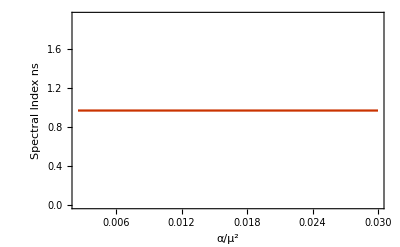

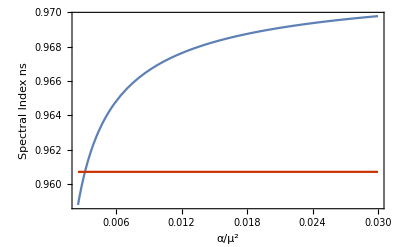

```mathematica
pn2=Plot[0.9607,{x,0.0025,0.03},Frame-> True,FrameLabel->{α/μ^2, "Spectral Index ns"},PlotStyle->112];
pn3=Plot[0.9691,{x,0.0025,0.03},Frame-> True,FrameLabel->{α/μ^2, "Spectral Index ns"},PlotStyle->112]
pn3=Show[pn1,pn2]
```

The second method is via contour plots:

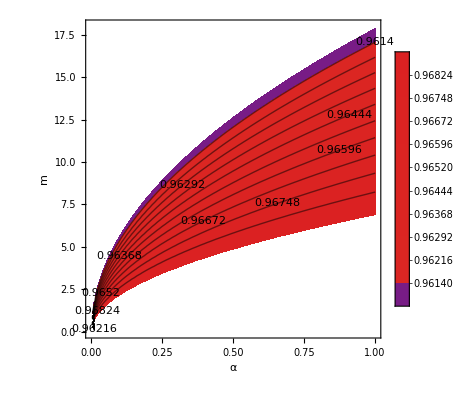

```mathematica
ContourPlot[ns60,{α,0,1},{μ,0.15,18},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10,PlotRange->{0.9607,0.9691}]
```

```mathematica
About the tensor to scalar ratio, r:
```

The first method is algebraically:

```mathematica
r60=r/. Y-> 60
```

((α μ^4)^(1/3))/(270 5^(2/3) 6^(1/3) α)

I set:α/μ^2 = x, thus the expression of the tensor to scalar ratio at the beginning of inflation assuming the latter lasted for Y=60 e-foldings, becomes:

```mathematica
r60'=x^(-2/3)/(270 5^(2/3) 6^(1/3))
```

1/(270 5^(2/3) 6^(1/3) x^(2/3))

```mathematica
Solve[r60'==0.056]
```

{{x→0.00138876}}

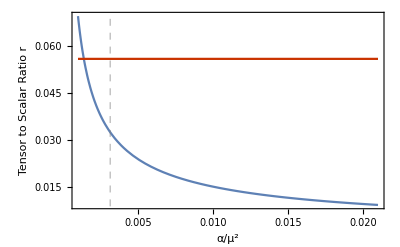

```mathematica
pr1=Plot[1/(270 5^(2/3) 6^(1/3) x^(2/3)),{x,0.001,0.0209707},PlotStyle->97,Frame-> True,FrameLabel->{α/μ^2, "Tensor to Scalar Ratio r"},PlotRange->Full,GridLines->{{0.0031378179558776875},{}},GridLinesStyle->Directive[Gray, Dashed]];
pr2=Plot[0.056,{x,0.001,0.0209707},PlotStyle->112,Frame-> True];
Show[pr1,pr2]
```

The second method is via contour plots:

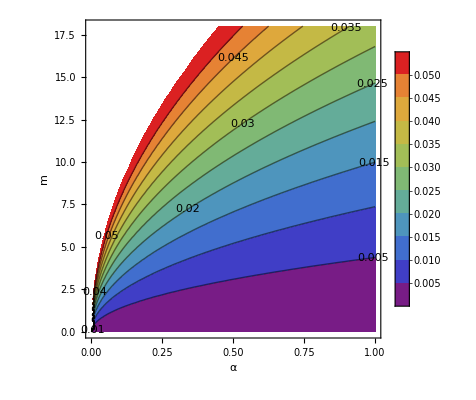

```mathematica
ContourPlot[r60,{α,0,1},{μ,10^(-6),18},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10,PlotRange->{0,0.056}]
```

```mathematica
About the first slow-roll index,ϵ1:
```

The first method is algebraically:

```mathematica
ϵ160=ϵ1i/. Y-> 60
```

((α μ^4)^(1/3))/(4320 5^(2/3) 6^(1/3) α)

I set:α/μ^2 = x

```mathematica
ϵ160'=x^(-2/3)/(4320 5^(2/3) 6^(1/3))
```

1/(4320 5^(2/3) 6^(1/3) x^(2/3))

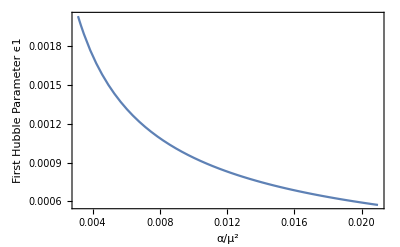

```mathematica
Plot[1/(4320 5^(2/3) 6^(1/3) x^(2/3)),{x,0.00313782,0.0209707},PlotStyle->97,Frame-> True,FrameLabel->{α/μ^2, "First Hubble Parameter ϵ1"},PlotRange->All]
```

The second method is via contour plots:

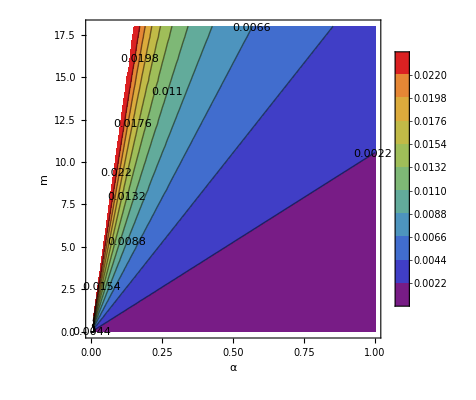

```mathematica
ContourPlot[μ/(4800 α),{α,0,1},{μ,10^(-6),18},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10]
```

```mathematica
(* The slow-roll approximation ϵ1<1 is satisfied for this range of values of the free parameters, that also satisfy the Planck contraints on ns and r *)
```

```mathematica
About the second slow-roll index,ϵ2:
```

The first method is algebraically:

```mathematica
ϵ260=ϵ2i/. Y-> 60 //Expand
```

1/72-μ^(4/5)/(25920 2^(1/5) α^(2/5))+((α μ^4)^(1/3))/(4320 5^(2/3) 6^(1/3) α)

I set:α/μ^2 = x

```mathematica
ϵ260'=1/72-x^(-2/5)/(25920 2^(1/5))+x^(-2/3)/(4320 5^(2/3) 6^(1/3))
```

1/72+1/(4320 5^(2/3) 6^(1/3) x^(2/3))-1/(25920 2^(1/5) x^(2/5))

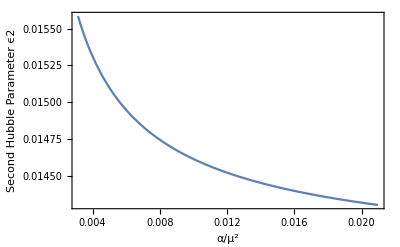

```mathematica
Plot[1/72+1/(4320 5^(2/3) 6^(1/3) x^(2/3))-1/(25920 2^(1/5) x^(2/5)),{x,0.00313782,0.0209707},PlotStyle->97,Frame-> True,FrameLabel->{α/μ^2, "Second Hubble Parameter ϵ2"},PlotRange->All]
```

The second method is via contour plots:

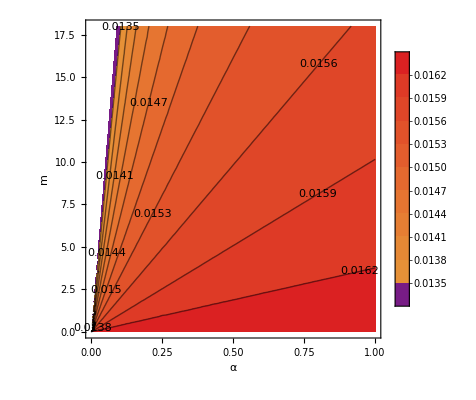

```mathematica
ContourPlot[1/60-(√μ)/(2400 √3 √α),{α,0,1},{μ,10^(-6),18},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10]
```

```mathematica
(* The slow-roll approximation ϵ2<1 is also satisfied for this range of values of the free parameters, that also satisfy the Planck contraints on ns and r *)
```

```mathematica
About the potential slow-roll index,ϵ:
```

```mathematica
ϵ60=ϵi/. Y-> 60
```

((α μ^4)^(1/3))/(4320 5^(2/3) 6^(1/3) α^2)

```mathematica
ϵ60'=x^(1/3)/(4320 5^(2/3) 6^(1/3))
```

x^(1/3)/(4320 5^(2/3) 6^(1/3))

```mathematica
Reduce[ϵ60'<0.01 && x>0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0<x<1.20932×10^7

```mathematica
Reduce[0.00005629560623293399μ^(4/5)<1 && μ>0,μ]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0<μ<205072.

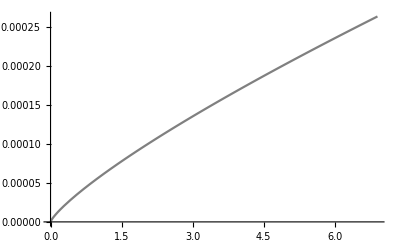

```mathematica
p1=Plot[0.00005629560623293399μ^(4/5),{μ,0,6.9054},PlotStyle->Gray]
```

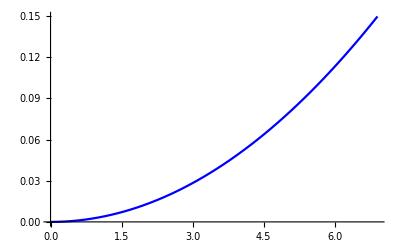

```mathematica
p2=Plot[0.00313782μ^2,{μ,0,6.9054},PlotStyle->Blue]
```

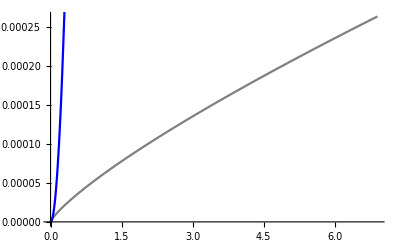

```mathematica
Show[p1,p2]
```

```mathematica
Solve[0.00313782μ^2==0.00005629560623293399μ^(4/5)]
```

{{μ→0.},{μ→0.0350649}}

```mathematica
Reduce[0.00313782μ^2<0.00005629560623293399μ^(4/5) && μ>0,μ]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0<μ<0.0350649

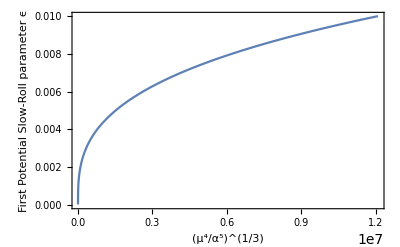

```mathematica
Plot[x^(1/3)/(4320 5^(2/3) 6^(1/3)),{x,0,1.20932352*^7},Frame-> True, FrameLabel->{(μ^4/α^5)^(1/3),"First Potential Slow-Roll parameter ϵ"}]
```

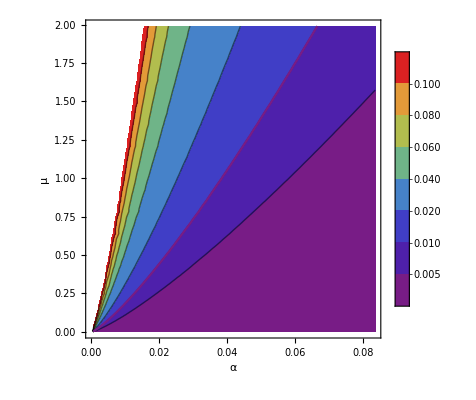

```mathematica
pe1=ContourPlot[((α μ^4)^(1/3))/(4320 5^(2/3) 6^(1/3) α^2),{α,0.0031378179558776875*10^(-12),0.08348550536775791},{μ,10^(-6),1.99},ColorFunction->"Rainbow",PlotLegends->Automatic, FrameLabel->{α,μ},Contours-> {0.1,0.08,0.06,0.04,0.02,0.01,0.005}];
pe2=ContourPlot[((α μ^4)^(1/3))/(4320 5^(2/3) 6^(1/3) α^2)==0.01,{α,0.0031378179558776875*10^(-12),0.08348550536775791},{μ,10^(-6),1.99},ColorFunction->"Rainbow",PlotLegends->Automatic, FrameLabel->{α,μ},Contours-> {0.1,0.08,0.06,0.04,0.02,0.01,0.005}];
Show[pe1,pe2]
```

```mathematica
About the potential slow-roll index,η:
```

```mathematica
ηi60=ηi/. Y-> 60 //Simplify
```

(-720 α^(2/5)+2^(4/5) μ^(4/5))/(51840 α^(7/5))

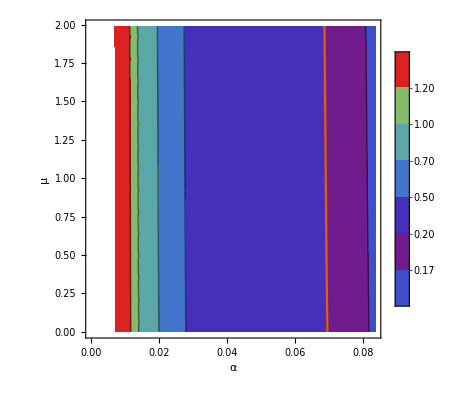

```mathematica
ph1=ContourPlot[Abs[(-720 α^(2/5)+2^(4/5) μ^(4/5))/(51840 α^(7/5))],{α,0.0031378179558776875*10^(-12),0.08348550536775791},{μ,10^(-6),1.99},ColorFunction->"Rainbow",PlotLegends->Automatic, FrameLabel->{α,μ},Contours->{0.7,1,1.2,0.5,0.2,0.08,0.05,0.17}];
ph2=ContourPlot[Abs[(-720 α^(2/5)+2^(4/5) μ^(4/5))/(51840 α^(7/5))]==0.2,{α,0.0031378179558776875*10^(-12),0.08348550536775791},{μ,10^(-6),1.99},PlotTheme->"Scientific",PlotLegends->Automatic, FrameLabel->{α,μ},Contours->{0.7,1,1.2,0.5,0.2,0.08,0.05,0.17}];Show[ph1,ph2]
```

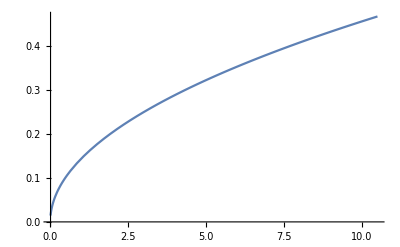

```mathematica
a=Plot[0.14433756729740646 √μ,{μ,10^(-2),10.5}]
```

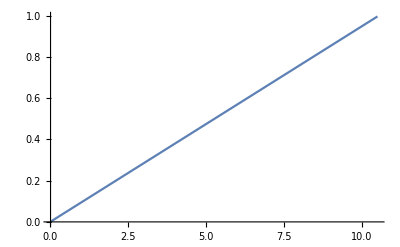

```mathematica
b=Plot[0.0949μ,{μ,10^(-2),10.5}]
```

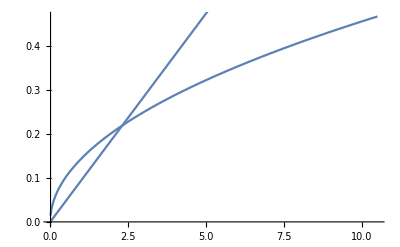

```mathematica
Show[a,b]
```

```mathematica
Solve[0.14433756729740646 √μ==0.0949μ,μ]
```

{{μ→0.},{μ→2.31327}}